```mathematica
NotebookDirectory[]
```

E:\cygwin\home\adewes\thesis\data\ct5\qubits - parameter surveys\igor export\

```mathematica
gammapurcell[κ_,g_,Δ_] := κ*g^2/(Δ^2+κ^2/4)
```

```mathematica
qubit1data=Import[NotebookDirectory[]<>"/qubit_1_summary.txt","Table"];
qubit1f01=qubit1data[[2;;,2]];
qubit1tpi=qubit1data[[2;;,4]];
qubit1trelax=qubit1data[[2;;,6]];
```

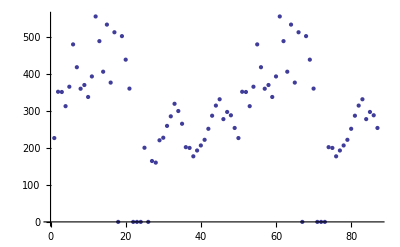

```mathematica
ListPlot[qubit1trelax]
```

```mathematica
qubit2data=Import[NotebookDirectory[]<>"/qubit_2.txt","Table"];
qubit2t1data=Import[NotebookDirectory[]<>"/qubit_2_t1.txt","Table"];
```

```mathematica
qubit1tpis=Map[{qubit1f01[[#]],1/qubit1tpi[[#]]}&,Range[1,Length[qubit1tpi]]];
qubit1Γpurcell=Map[{qubit1f01[[#]],1/qubit1trelax[[#]]}&,Range[1,Length[qubit1tpi]]];
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

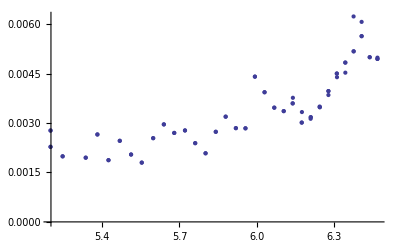

```mathematica
ListPlot[qubit1Γpurcell]
```

```mathematica
qubit1rabif = 0.0085*2*Sqrt[2]*800/Sqrt[1+4*800^2*(f/6.82-1)^2]
```

19.2333/(√(1+2560000 (-1+0.146628 f)^2))

```mathematica
values = Map[{#,qubit1rabif /.{f->#}}&,Range[5,6.5,0.001]];
Export[NotebookDirectory[]<>"qubit1_rabi_theory.csv",values,"CSV"]
```

E:\cygwin\home\adewes\thesis\data\ct5\qubits - parameter surveys\igor export\qubit1_rabi_theory.csv

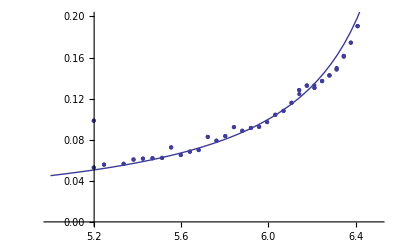

```mathematica
Show[ListPlot[qubit1tpis],Plot[qubit1rabif,{f,5,6.5}],PlotRange->{0,0.2}]
```

```mathematica
qubit2t1data[[1]]
```

{f0,vcoil,T1}

```mathematica
qubit2flux=qubit2data[[2;;,1]];
qubit2f01=qubit2data[[2;;,2]];
qubit2f02=qubit2data[[2;;,3]];
qubit2tpi=qubit2data[[2;;,4]];
qubit2contrast10=qubit2data[[2;;,5]];
qubit2t1=qubit2data[[2;;,6]];
qubit2t2=qubit2data[[2;;,7]];
qubit2t12=qubit2t1data[[2;;,3]];
qubit2f012=qubit2t1data[[2;;,1]];
```

```mathematica
gammas2=Map[{qubit2f012[[#]],1/qubit2t12[[#]]}&,Range[1,Length[qubit2t12]]];
rabi2=Map[{qubit2f012[[#]],qubit2tpi[[#]]}&,Range[1,Length[qubit2tpi]]];
```

1/2 (50.+(29 ⅈ f π)/500)

25.+0.455531 ⅈ

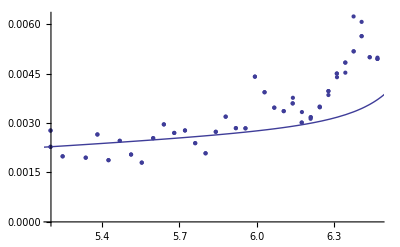

```mathematica
l=29*^-3;
zfl1 = 1/(1/(50.+I*2π*f*l)+1/(50.+I*2π*f*l))
zfl1 /.{f->5}
flrelax1 = 16*π*(3/40)^2*2π*0.5^2*f*Re[zfl1]/rk;
purcellrelax1=(gammapurcell[κ,g,Δ]/1*^9+0.00) /.{κ->6.85*^9*2π/800,g->50*^6*2π,Δ->2π*Abs[f*1*^9+-6.85*^9]};
relaxtot1 = flrelax1+purcellrelax1;
values = Map[{#,relaxtot1,flrelax1,purcellrelax1 }/.{f->#}&,Range[5,6.5,0.001]];
Export[NotebookDirectory[]<>"qubit1_relax_theory.csv",values,"CSV"];
Show[ListPlot[qubit1Γpurcell],Plot[relaxtot1,{f,5,6.5}]]
```

1583.92/(√(1+2560000 (-1+0.149254 f)^2))

E:\cygwin\home\adewes\thesis\data\ct5\qubits - parameter surveys\igor export\qubit2_rabi_theory.csv

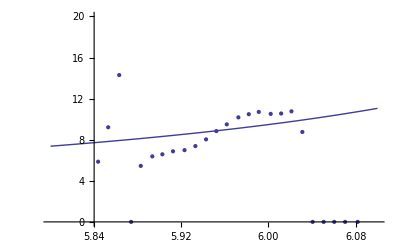

```mathematica
qubit2rabif=0.7*2*Sqrt[2]*800/Sqrt[1+4*800^2*(f/6.7-1)^2]
values = Map[{#,qubit2rabif /.{f->#}}&,Range[5,6.5,0.001]];
Export[NotebookDirectory[]<>"qubit2_rabi_theory.csv",values,"CSV"]
Show[ListPlot[rabi2],Plot[qubit2rabif,{f,5.8,6.1}],PlotRange->{0,20}]
```

```mathematica
6.7*^9*2π/800
```

```mathematica
5.2621676947629035*^7
```

5.26217×10^7

```mathematica
Solve[0.001==gammapurcell[κ,g,Δ]/1*^9 /.{κ->6.7*^9*2π/800,g->50*^6*2π,Δ->2π*Abs[f*1*^9+-6.7*^9]},f]
```

{{f→6.33732},{f→7.06268}}

E:\cygwin\home\adewes\thesis\data\ct5\qubits - parameter surveys\igor export\qubit2_relax_theory.csv

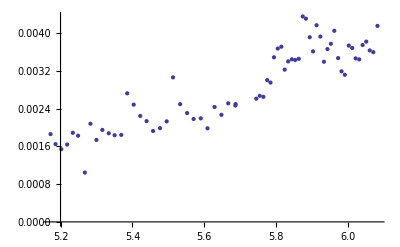

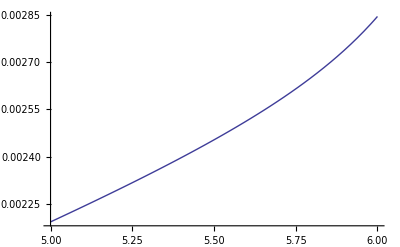

```mathematica
kb=1.38 10^(-23);
e=1.6 10^-19;
h=6.62 10^-34;
zfl2 = 25.;
flrelax2 = 16*π*(3./40)^2*2π*0.5^2*f/rk*zfl2;
purcellrelax2=(gammapurcell[κ,g,Δ]/1*^9+0.00) /.{κ->6.7*^9*2π/800,g->50*^6*2π,Δ->2π*Abs[f*1*^9+-6.7*^9]};
relaxtot2 = flrelax2+purcellrelax2;
values = Map[{#,relaxtot2,flrelax2,purcellrelax2 }/.{f->#}&,Range[5,6.5,0.001]];
Export[NotebookDirectory[]<>"qubit2_relax_theory.csv",values,"CSV"]
pl1=ListPlot[gammas2]
pl2=Plot[relaxtot2,{f,5,6},PlotRange->Full]
```

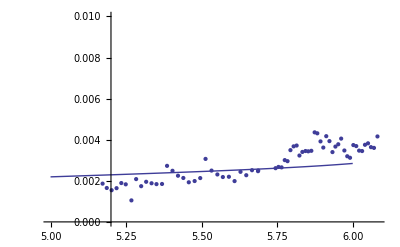

```mathematica
Show[pl1,pl2,PlotRange->{0,0.01}]
```

```mathematica
1./gammapurcell[44*2π*1*^6,107*^6*2π,(5.17-4)*1*^9*2π]*1*^9
```

432.638

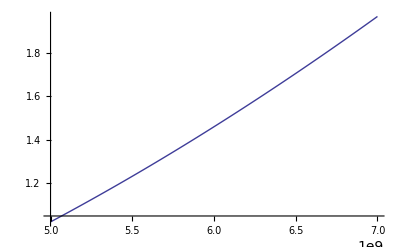

```mathematica
Plot[1/(1/50+50/((2π*f*230*^-12)^2)),{f,5*^9,7*^9}]
```

```mathematica
2.π*5*^9*250*^-12
```

7.85398